# Simplify Integrand

```mathematica
a T^4 u^3/(Exp[u]-1) * (1-Exp[-u])/(T^(7/2)u^3)
```

(a (1-ⅇ^-u) √T)/(-1+ⅇ^u)

```mathematica
Integrate[a c/(4π) 15/π^4 u^3/(Exp[u/T]-1),{u,0,∞}]
```

ConditionalExpression[(a c T^4)/(4 π), Re[T]>0]

```mathematica
Simplify[a c  T^4 u^3/(Exp[u]-1)15/π^4 * (1-Exp[-u])/(T^(7/2)u^3)]
```

(15 a c ⅇ^-u √T)/π^4

```mathematica
TeXForm[%]
```

\frac{15 a \sqrt{T} e^{-u}}{\pi ^4}

```mathematica
Integrate[(15 a c ⅇ^-u √T)/π^4,{u,0,∞}]
```

(15 a c √T)/π^4

```mathematica
TeXForm[%]
```

\frac{15 a \sqrt{T}}{\pi ^4}

```mathematica
Integrate[(1-Exp[-u])/(T^(7/2)u^3) a c T^4 u^3/(Exp[u]-1)15/π^4,{u,0,∞}]
```

(15 a c √T)/π^4

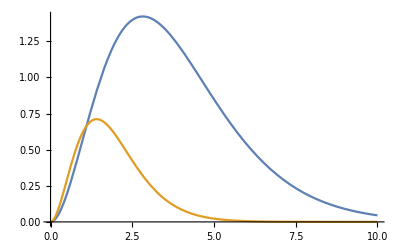

```mathematica
Plot[{T^3 (u/T)^3/(Exp[(u/T)]-1)/.T->1,T^4  Tl^4(u/Tl)^3/(Exp[(u/Tl)]-1)/.{T->1,Tl-> 0.5}},{u,0,10}]
```

```mathematica
ϕu = a c Tra^4 15/(π^4 Tc)(u/Tc)^3/(Exp[u/Tc]-1)
```

(15 a c Tra^4 u^3)/((-1+ⅇ^(u/Tc)) π^4 Tc^4)

```mathematica
Simplify[ a c Tra^4 15/(π^4 Tc)(u/Tc)^3/(Exp[u/Tc]-1)]
```

(15 a c Tra^4 u^3)/((-1+ⅇ^(u/Tc)) π^4 Tc^4)

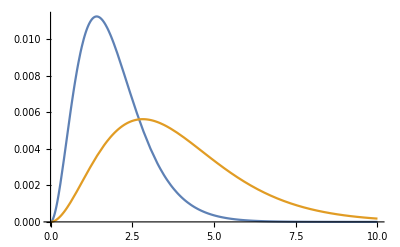

```mathematica
Plot[{ϕu/.{a-> 0.0137202,c->29.979245830, Tra-> 0.5,Tc-> 0.5},ϕu/.{a-> 0.0137202,c->29.979245830, Tra-> 0.5,Tc-> 1.0}},{u,0,10}]
```

```mathematica
Assuming[Tc>0,Integrate[ϕu,{u,0,∞}]]
```

a c Tra^4

```mathematica
Assuming[T>0,Integrate[(15 a c)/π^4(u)^3/(Exp[u/T]-1),{u,0,∞}]]
```

a c T^4

```mathematica
D[ϕu,u]
```

(45 a c T^4 u^2)/((-1+ⅇ^(u/Tc)) π^4 Tc^4)-(15 a c ⅇ^(u/Tc) T^4 u^3)/((-1+ⅇ^(u/Tc))^2 π^4 Tc^5)

```mathematica
Assuming[Tc>0,Integrate[ϕu * (u),{u,0,∞}]]
```

(360 a c Tc Tr^4 Zeta[5])/π^4

```mathematica
Assuming[Tc>0,Integrate[(1-Exp[-u/T])/(T^(7/2)(u/T)^3) * ((15 a c)/π^4(u)^3/(Exp[u/T]-1)),{u,0,∞}]]
```

ConditionalExpression[(15 a c √T)/π^4, Re[T]>0]

```mathematica
Assuming[Tc>0&&T>0,Integrate[(1-Exp[-u/T])/(T^(7/2)(u/T)^3) * ((a c Tr^4 15)/(π^4 Tc)(u/Tc)^3/(Exp[u/Tc]-1)),{u,0,∞}]]
```

(15 a c Tr^4 HarmonicNumber[Tc/T])/(π^4 √T Tc^3)

```mathematica
Assuming[Tc>0&&T>0,Integrate[(1-Exp[-u/T])/(T^(7/2)(u/T)^3) * (15/π^4(u/T)^3/(Exp[u/T]-1)),{u,0,∞}]]
```

```mathematica
DE1 = a  D[Tra[t]^4,t] == -a c Tra[t]^4 (15 HarmonicNumber[Tc[t]/T[t]])/(π^4 √T[t] Tc[t]^3)+(15 a c √T[t])/π^4/.Tr[t]-> Tra[t]
```

4 a Tra[t]^3 Tra'[t]==(15 a c √T[t])/π^4-(15 a c HarmonicNumber[Tc[t]/T[t]] Tra[t]^4)/(π^4 √T[t] Tc[t]^3)

```mathematica
DEMat = D[T[t],t]==  a c Tr[t]^4 (15 HarmonicNumber[Tc[t]/T[t]])/(π^4 √T[t] Tc[t]^3)-(15 a c √T[t])/π^4/.Tr[t]-> Tra[t]
```

T'[t]==-(15 a c √T[t])/π^4+(15 a c HarmonicNumber[Tc[t]/T[t]] Tra[t]^4)/(π^4 √T[t] Tc[t]^3)

```mathematica
Simplify[(a c Tr[t]^4 (15 HarmonicNumber[Tc[t]/T[t]])/(π^4 √T[t] Tc[t]^3)-(15 a c √T[t])/π^4/.Tr[t]-> Tra[t])+( -a c Tra[t]^4 (15 HarmonicNumber[Tc[t]/T[t]])/(π^4 √T[t] Tc[t]^3)+(15 a c √T[t])/π^4/.Tr[t]-> Tra[t])]
```

0

#### Abs * nu

```mathematica
Assuming[Tc>0&&T>0,Integrate[u(1-Exp[-u/T])/(T^(7/2)(u/T)^3) * ((a c Tr^4 15)/(π^4 Tc)(u/Tc)^3/(Exp[u/Tc]-1)),{u,0,∞}]]
```

(5 a c Tr^4 (π^2-6 Zeta[2,(T+Tc)/T]))/(2 π^4 √T Tc^2)

```mathematica
Emiss*nu
```

```mathematica
Assuming[Tc>0 && T>0,Integrate[u(1-Exp[-u/T])/(T^(7/2)(u/T)^3) * ((15 a c)/π^4(u)^3/(Exp[u/T]-1)),{u,0,∞}]]
```

(15 a c T^(3/2))/π^4

```mathematica
DE2 = 1/c D[(360 a c Tra[t]^4 Tc[t] Zeta[5])/π^4,t] == -(5 a c Tra[t]^4 (π^2-6 Zeta[2,(T[t]+Tc[t])/T[t]]))/(2 π^4 √T[t] Tc[t]^2)+(15 a c T[t]^(3/2))/π^4/.Tr[t]-> Tra[t]
```

((360 a c Tra[t]^4 Zeta[5] Tc'[t])/π^4+(1440 a c Tc[t] Tra[t]^3 Zeta[5] Tra'[t])/π^4)/c==(15 a c T[t]^(3/2))/π^4-(5 a c Tra[t]^4 (π^2-6 Zeta[2,(T[t]+Tc[t])/T[t]]))/(2 π^4 √T[t] Tc[t]^2)

```mathematica
Tfunc=NDSolve[{DE1/.{a-> 0.0137202,c->29.979245830},DE2/.{a-> 0.0137202,c->29.979245830},DEMat/.{a-> 0.0137202,c->29.979245830},Tc[0]==.5,Tra[0]==0.5, T[0]== 0.4},{Tc,Tra,T},{t,0,1}]
```

{{Tc→InterpolatingFunction[…],Tra→InterpolatingFunction[…],T→InterpolatingFunction[…]}}

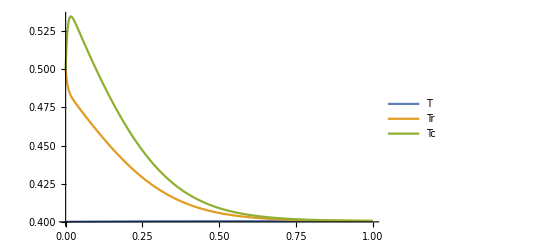

```mathematica
Plot[Evaluate[{T[t],Tra[t],Tc[t]}/.Tfunc],{t,0,1},PlotRange->All,PlotLegends->LineLegend[{"T","Tr","Tc"}]]
```

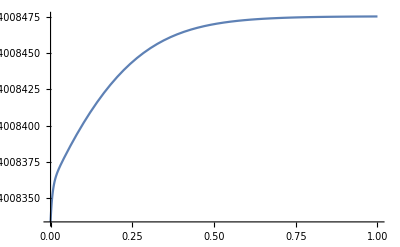

```mathematica
Plot[Evaluate[T[t] +  4/300*Tra[t]^4/.Tfunc],{t,0,1}]
```

```mathematica
Evaluate[(15 a c)/π^4(u)^3/(Exp[u/Tra[t]]-1)/.T-> T[t]/.Tfunc]/.t-> 0.1/.{a-> 4/30,c-> 30}
```

{(60 u^3)/((-1+ⅇ^(2.16941 u)) π^4)}

```mathematica
{Tra[0.1],Tc[0.1]}/.Tfunc
```

{{0.460955,0.499322}}

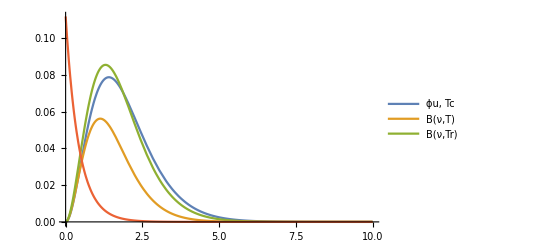

```mathematica
Plot[{Evaluate[ϕu/.{Tra-> Tra[t],Tc->Tc[t] }/.Tfunc]/.t-> 0.1/.{a-> 4/30,c-> 30}, Evaluate[(15 a c)/π^4(u)^3/(Exp[u/T]-1)/.T-> T[t]/.Tfunc]/.t-> 0.1/.{a-> 4/30,c-> 30},Evaluate[(15 a c)/π^4(u)^3/(Exp[u/Tra]-1)/.Tra-> Tra[t]/.Tfunc]/.t-> 0.1/.{a-> 4/30,c-> 30},(Evaluate[(1-Exp[-u/T])/(T^(7/2)(u/T)^3)(15 4)/π^4(u)^3/(Exp[u/Tra]-1)/.{T->T[t],Tra-> Tra[t]}/.Tfunc])/10/.t->0.1},{u,0.001,10},PlotRange->All,PlotLegends->LineLegend[{"ϕu, Tc","B(ν,T)","B(ν,Tr)"}]]
```

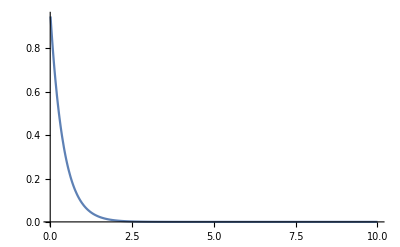

```mathematica
Plot[(Evaluate[(1-Exp[-u/T])/(T^(7/2)(u/T)^3)(15 4)/π^4(u)^3/(Exp[u/T]-1)/.T-> T[t]/.Tfunc])/.t->0.1,{u,10^-2,10},PlotRange->All]
```

```mathematica
Limit[(1-Exp[-u/T])/(T^(7/2)(u/T)^3),u-> 0]
```

DirectedInfinity[1/Sign[T]]/(√T)

```mathematica
"
```

```mathematica
Plot[ϕu
```

```mathematica
Integrate[ϕu/.{Tra-> 1/2,Tc-> 1/2},{u,0,∞}]
```

(a c)/16

```mathematica
{DE1,DE2,DEMat}/.{a->4/30,c-> 30,t->0}/.{Tra[0]-> 0.5,T[0]-> 0.4,Tc[0]-> 0.5}
```

{0.0666667 Tra'[0]==-0.17032,0.958057 Tc'[0]+3.83223 Tr'[0]==-0.108982,T'[0]==0.17032}

```mathematica
D[ a c T[t]^4 15/(π^4 Tc[t])(u/Tc[t])^3/(Exp[u/Tc[t]]-1),t]
```

(60 a c u^3 T[t]^3 T'[t])/((-1+ⅇ^(u/Tc[t])) π^4 Tc[t]^4)+(15 a c ⅇ^(u/Tc[t]) u^4 T[t]^4 Tc'[t])/((-1+ⅇ^(u/Tc[t]))^2 π^4 Tc[t]^6)-(60 a c u^3 T[t]^4 Tc'[t])/((-1+ⅇ^(u/Tc[t])) π^4 Tc[t]^5)

```mathematica
Assuming[Tc[t]>0,Integrate[(60 a c u^3 T[t]^3 T'[t])/((-1+ⅇ^(u/Tc[t])) π^4 Tc[t]^4)+(15 a c ⅇ^(u/Tc[t]) u^4 T[t]^4 Tc'[t])/((-1+ⅇ^(u/Tc[t]))^2 π^4 Tc[t]^6)-(60 a c u^3 T[t]^4 Tc'[t])/((-1+ⅇ^(u/Tc[t])) π^4 Tc[t]^5),{u,0,∞}]]
```

$Aborted